# A CGS-QE computation in the inverse kinematic problem

## Solving the inverse kinematic problem: an example

Akira Terui

This file provides a computation in the inverse kinematic problem with the CGS-QE algorithm appearing in the paper:
Shuto Otaki, Akira Terui and Masahiko Mikawa,
A Design and an Implementation of an In- verse Kinematics Computation in Robotics Using Real Quantifier Elimination based on Comprehensive Gröbner Systems.

```mathematica
c1[theta1_]:=Cos[theta1]
```

```mathematica
s1[theta1_]:=Sin[theta1]
```

```mathematica
c4[theta4_] := Cos[theta4]
```

```mathematica
s4[theta4_]:= Sin[theta4]
```

```mathematica
c7[theta7_]:=Cos[theta7]
```

```mathematica
s7[theta7_]:=Sin[theta7]
```

```mathematica
x[theta1_,theta4_,theta7_] := -112 c1[theta1]c4[theta4]s7[theta7] +16c1[theta1]c4[theta4]-112c1[theta1]s4[theta4]c7[theta7]-136c1[theta1]s4[theta4]+44Sqrt[2]c1[theta1]
```

```mathematica
y[theta1_,theta4_,theta7_] := -112 s1[theta1]c4[theta4]s7[theta7] +16s1[theta1]c4[theta4]-112s1[theta1]s4[theta4]c7[theta7]-136s1[theta1]s4[theta4]+44Sqrt[2]s1[theta1]
```

```mathematica
z[theta1_,theta4_,theta7_] := 112 c4[theta4]c7[theta7] +136c4[theta4]-112s4[theta4]s7[theta7]+16s4[theta4]+104+44Sqrt[2]
```

```mathematica
N[Pi/2]
```

1.5708

## Drawing a feasible region

For t1=θ_1=-1.5(≃-π/2),... , 1.5(≃π/2), t2=θ_2=-1.5(≃-π/2),... , 1.5(≃π/2), t3=θ_3=-1.5(≃-π/2),... , 1.5(≃π/2), we have plotted the position of the end-effector in the  ℝ^3  space.

```mathematica
data1 =Flatten[Table[{N[x[t1,t4,t7]],N[y[t1,t4,t7]],N[z[t1,t4,t7]]}, {t1,-1.5,1.5,0.1},{t4,-1.5,1.5,0.1},{t7,-1.5,1.5,0.1}],1]
```

{{{15.1959,-214.284,49.0066},{15.9733,-225.247,51.1384},{16.7318,-235.943,54.3568},{17.4638,-246.265,58.6297},24,{15.6518,-220.713,269.653},{14.8688,-209.671,271.326},{14.0779,-198.518,271.886}},959,{1}}
 |  |  |  |

```mathematica
ListPointPlot3D[data1,AxesLabel->{x,y,z},BaseStyle->{FontSize->20}]
```

-Graphics3D-

Next, we have fixed t1=θ_1=0 and by moving  t2=θ_2=-1.5(≃-π/2),... , 1.5(≃π/2), t3=θ_3=-1.5(≃-π/2),... , 1.5(≃π/2), we have plotted the position of the end-effector on the x z- plane.

```mathematica
data2 =Flatten[Table[{N[x[0,t4,t7]],N[z[0,t4,t7]]}, {t1,0,1.5,0.1},{t4,-1.5,1.5,0.1},{t7,-1.5,1.5,0.1}],2];
```

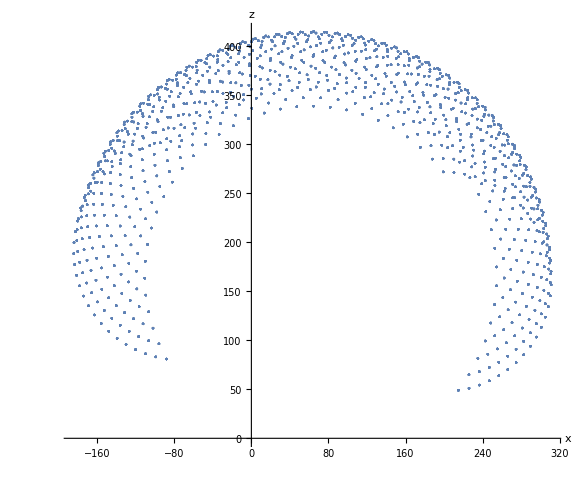

```mathematica
ListPlot[data2,AspectRatio->Automatic,AxesLabel->{x,z},BaseStyle->{FontSize->30}]
```

## Deriving the forward kinematic problem

We verify deriving the forward kinematic problem described in Section 2.
Let Ti be the matrix ^(i-1)T_i defined in Page 6.

```mathematica
T[a_,alpha_,d_,t_] :=({{1, 0, 0, a}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).({{1, 0, 0, 0}, {0, Cos[alpha], -Sin[alpha], 0}, {0, Sin[alpha], Cos[alpha], 0}, {0, 0, 0, 1}}).({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, d}, {0, 0, 0, 1}}).({{Cos[t], -Sin[t], 0, 0}, {Sin[t], Cos[t], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
```

```mathematica
T[a,al,d,t]
```

{{Cos[t],-Sin[t],0,a},{Cos[al] Sin[t],Cos[al] Cos[t],-Sin[al],-d Sin[al]},{Sin[al] Sin[t],Cos[t] Sin[al],Cos[al],d Cos[al]},{0,0,0,1}}

```mathematica
MatrixForm[%]
```

(Cos[t] | -Sin[t] | 0 | a
Cos[al] Sin[t] | Cos[al] Cos[t] | -Sin[al] | -d Sin[al]
Sin[al] Sin[t] | Cos[t] Sin[al] | Cos[al] | d Cos[al]
0 | 0 | 0 | 1)

```mathematica
T1 = T[0,0,80,t1]
```

{{Cos[t1],-Sin[t1],0,0},{Sin[t1],Cos[t1],0,0},{0,0,1,80},{0,0,0,1}}

```mathematica
T2 = T[0,Pi/2,0,Pi/4]
```

{{1/(√2),-1/(√2),0,0},{0,0,-1,0},{1/(√2),1/(√2),0,0},{0,0,0,1}}

```mathematica
T3 = T[88,0,0,Pi/4]
```

{{1/(√2),-1/(√2),0,88},{1/(√2),1/(√2),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
T4 = T[24,0,0,t4]
```

{{Cos[t4],-Sin[t4],0,24},{Sin[t4],Cos[t4],0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
T5 = T[96,0,0,-Pi/2]
```

{{0,1,0,96},{-1,0,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
T6 = T[16,0,0,Pi/2]
```

{{0,-1,0,16},{1,0,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
T7 = T[40,0,0,t7]
```

{{Cos[t7],-Sin[t7],0,40},{Sin[t7],Cos[t7],0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
T8 = T[112,0,0,0]
```

{{1,0,0,112},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
TT = T1.T2.T3.T4.T5.T6.T7.T8
```

{{-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7],-Cos[t1] Cos[t4] Cos[t7]+Cos[t1] Sin[t4] Sin[t7],Sin[t1],44 √2 Cos[t1]+16 Cos[t1] Cos[t4]-136 Cos[t1] Sin[t4]+112 (-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7])},{-Cos[t7] Sin[t1] Sin[t4]-Cos[t4] Sin[t1] Sin[t7],-Cos[t4] Cos[t7] Sin[t1]+Sin[t1] Sin[t4] Sin[t7],-Cos[t1],44 √2 Sin[t1]+16 Cos[t4] Sin[t1]-136 Sin[t1] Sin[t4]+112 (-Cos[t7] Sin[t1] Sin[t4]-Cos[t4] Sin[t1] Sin[t7])},{Cos[t4] Cos[t7]-Sin[t4] Sin[t7],-Cos[t7] Sin[t4]-Cos[t4] Sin[t7],0,104+44 √2+136 Cos[t4]+16 Sin[t4]+112 (Cos[t4] Cos[t7]-Sin[t4] Sin[t7])},{0,0,0,1}}

```mathematica
MatrixForm[TT]
```

(-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7] | -Cos[t1] Cos[t4] Cos[t7]+Cos[t1] Sin[t4] Sin[t7] | Sin[t1] | 44 √2 Cos[t1]+16 Cos[t1] Cos[t4]-136 Cos[t1] Sin[t4]+112 (-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7])
-Cos[t7] Sin[t1] Sin[t4]-Cos[t4] Sin[t1] Sin[t7] | -Cos[t4] Cos[t7] Sin[t1]+Sin[t1] Sin[t4] Sin[t7] | -Cos[t1] | 44 √2 Sin[t1]+16 Cos[t4] Sin[t1]-136 Sin[t1] Sin[t4]+112 (-Cos[t7] Sin[t1] Sin[t4]-Cos[t4] Sin[t1] Sin[t7])
Cos[t4] Cos[t7]-Sin[t4] Sin[t7] | -Cos[t7] Sin[t4]-Cos[t4] Sin[t7] | 0 | 104+44 √2+136 Cos[t4]+16 Sin[t4]+112 (Cos[t4] Cos[t7]-Sin[t4] Sin[t7])
0 | 0 | 0 | 1)

```mathematica
TT[[1]]
```

{-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7],-Cos[t1] Cos[t4] Cos[t7]+Cos[t1] Sin[t4] Sin[t7],Sin[t1],44 √2 Cos[t1]+16 Cos[t1] Cos[t4]-136 Cos[t1] Sin[t4]+112 (-Cos[t1] Cos[t7] Sin[t4]-Cos[t1] Cos[t4] Sin[t7])}